# Discriminants

Author: Jens Forsgård
Latest version: February 2020

```mathematica
BeginPackage[ "Discriminants`"];
Needs["ComputationalGeometry`"];
```

```mathematica
Gale::usage = "Gale[ A] returns a Gale dual of a point configuration A."

CuspidalForm::usage = "CuspidalForm[ A] returns the Cuspidal Form of the A-Discriminant. 
Uses an arbitrary Gale Dual (i.e., choice of coordinates) unless one is specified."

DualDefectiveQ::usage = "DualDefectiveQ[ A] returns a boolean value encoding if the points configuration A is dual defective."

HornKapranov::usage = "HornKapranov[ A] returns the Horn--Kapranov uniformization map of the A-Discriminant.
Uses an arbitrary Gale Dual (i.e., choice of coordinates) unless one is specified."

ADiscriminant::usage = "ADiscriminant[ A] returns the A-Discriminant polynomial of an integral point configuration A, encoded by an integer matrix.
Uses Greobner Basis techniques."

UniADiscriminant::usage = "UniADiscriminant[ A] returns the A-Discriminant polynomial of an integral point configuration A, encoded by a integer matrix of rank 2.
The algorithm is significantly faster then the algorithm used inthe function ADiscriminant[ A]."

NewtonPolytopePlot::usage = "NewtonPolytopePlot[ func] returns a plot of the Newton Polytope of the (bivariate) polynomial func."

ConvexHullPlot::usage = "ConvexHullPlot[ A] returns a plot of the Newton Polytope (i.e., convex hull) of the point congifuration A."
```

```mathematica
Begin["Private`"];
```

## Minor Functions

```mathematica
Gale[A_] := NullSpace[A]ᵀ;
```

```mathematica
HomogenizeA[A_] := Prepend[A, ConstantArray[1, Length[First[A]]]];
```

```mathematica
HomogeneousQ[A_] := (MatrixRank[A] == MatrixRank[HomogenizeA[A]])
```

```mathematica
FullRankQ[A_] := (MatrixRank[A] == Min[Length[A], Length[First[A]]])
```

## CuspidalForm

```mathematica
Options[CuspidalForm]=
	{
		"GaleDual" -> {},
		"VariableName" -> Global`t,
		"CheckInput" -> True
	};

CuspidalForm[A_, OptionsPattern[]] := Module[{AA, AT, AH, BT, SS, tt},
	
	CuspidalForm::VariableName = "Variable name has an assigned value.";
	CuspidalForm::Homogeneous = "The point configuration A is not homogeneous.";
	CuspidalForm::FullRank = "The matrix representation of A does not have full rank.";
	CuspidalForm::Modified = "The configuration A is not in standard form. Continuing with `1`.";
	
	If[OptionValue["CheckInput"],
		If[Not[Head[OptionValue["VariableName"]]===Symbol],
			Message[CuspidalForm::VariableName];
			Return[$Failed]];
		If[Not[HomogeneousQ[A]],
			Message[CuspidalForm::Homogeneous];
			Return[$Failed]];
		If[Not[FullRankQ[A]],
			Message[CuspidalForm::FullRank];
			Return[$Failed]];];
	
	AA = Drop[A, 1];
	AT = AAᵀ;
	If[DeleteDuplicates[First[A]] ≠ {1}, 
		AH = HomogenizeA[AA]; Message[CuspidalForm::Modified, AH];,
		AH = A];
	tt = Table[Indexed[OptionValue["VariableName"], j], {j, 1, Length[AT] - Length[AH]}];
	If[OptionValue["GaleDual"]=={},  BT = Gale[AH].tt, BT = OptionValue["GaleDual"].tt];
   
   SS = Subsets[Range[Length[AT]], {Length[AA]}];
   (Det[AT[[#]]]^2 * (Times@@(BT[[#]])) & /@ SS)  // Total // Expand // Return
   
];
```

## DualDefectiveQ

```mathematica
DualDefectiveQ[A_] := Module[{t, tt, cuspidalForm},

	DualDefectiveQ::Homogeneous = "The point configuration A is not homogeneous.";
	DualDefectiveQ::FullRank = "The matrix representation of A does not have full rank.";
	
	If[Not[HomogeneousQ[A]],
		Message[DualDefectiveQ::Homogeneous];
		Return[$Failed]];
	If[Not[FullRankQ[A]],
		Message[DualDefectiveQ::FullRank];
		Return[$Failed]];

	(* Compute the cuspidal form and check if it is the zero polynomial. *)
	tt = Table[Indexed[t, j], {j, 1, Length[Aᵀ] - Length[A]}];
	cuspidalForm = CuspidalForm[A, "GaleDual" -> Gale[A], "VariableName" -> t, "CheckInput" -> False];
    If[Length[CoefficientRules[cuspidalForm, tt]] == 0, Return[True], Return[False]]

];
```

## HornKapranov

```mathematica
Options[HornKapranov] =
	{
		"GaleDual" -> {},
		"KernelParameter" ->  Global`t,
		"ToricParameter" ->  Global`z
	};

HornKapranov[A_, OptionsPattern[]] := Module[{BT, tt, zz},

	HornKapranov::Parameter = "The parameter given for the `1` has an assigned value.";
	HornKapranov::Homogeneous = "The point configuration is not homogeneous.";
	
	If[Not[TrueQ[Head[OptionValue["KernelParameter"]]===Symbol]],
		Message[HornKapranov::Parameter, "kernel parameter"];
		Return[$Failed]];
	If[Not[TrueQ[Head[OptionValue["ToricParameter"]]===Symbol]],
		Message[HornKapranov::Parameter, "toric parameter"];
		Return[$Failed]];
	If[Not[HomogeneousQ[A]],
		Message[HornKapranov::Homogeneous];
		Return[$Failed]];

	If[Length[Aᵀ] == Length[A], Return[Null]];
	
	tt = Table[Indexed[OptionValue["KernelParameter"], j], {j, 1, Length[Aᵀ] - MatrixRank[A]}];
	zz = Table[Indexed[OptionValue["ToricParameter"], j], {j, 1, Length[A]-1}];
	
	If[OptionValue["GaleDual"] == {} , BT = Gale[A].tt;,  BT = OptionValue["GaleDual"].tt;];
	
	Return[(Times@@(zz^#) & /@ (Drop[A, 1]ᵀ)) * BT];

];
```

## ADiscriminant

```mathematica
Options[ADiscriminant]=
	{
		"VariableName" ->  Global`x
	};

ADiscriminant[A_, OptionsPattern[]]:=
	Module[{defective, BT, t, tt, z, zz, xx, AdjustRow},

	ADiscriminant::Parameter = "The chosen variable name has an assigned value.";
	ADiscriminant::Defective = "The point configuration A is dual defective.";

	If[Not[TrueQ[Head[OptionValue["VariableName"]] == Symbol]],
		Message[ADiscriminant::Parameter];
		Return[$Failed]];
	
	defective = DualDefectiveQ[A];
	If[defective == $Failed, Return[$Failed]];
	If[TrueQ[defective],
		Message[ADiscriminant::Defective];
		Return[$Failed]];
	
	AdjustRow[r_] := Module[{entries},
		entries = DeleteDuplicates[r];
		If[Length[entries] == 1, 
			Return[r/First[entries]],
			Return[r - Min[r]*ConstantArray[1,Length[r]]]]];

	If[Min[Flatten[A]] < 0, A = AdjustRow /@ A];

	tt = Table[Indexed[t, j], {j, 1, Length[Aᵀ] - Length[A]}];
	zz = Table[Indexed[z, j], {j, 1, Length[A]-1}];
	xx = Table[Indexed[OptionValue["VariableName"],j],{j,1,Length[Aᵀ]}];
  
	GroebnerBasis[HornKapranov[A, "GaleDual" -> Gale[A], "KernelParameter" -> t, "ToricParameter" -> z] - xx,
		xx, Join[tt,zz]] // First // Return;

];
```

## UniADiscriminant

```mathematica
(* Private iterative process for constructing all tuples whose total sum is below some treshhold. *)
PointCreator[head_, ranges_, bound_] := Module[{range, new},
	range = Select[ranges // First, # ≤ bound &];
	If[Length[ranges] == 1,
		Return[Append[head, #]& /@ range];,
		Return[Flatten[PointCreator[Append[head, #], Drop[ranges, 1], bound - #]& /@ range, 1]]
	];
];
```

```mathematica
(* Private function PointsInPolytope returns a list all points inside of the polytope
	with vertives given in the list _vertices_. We provide as input also the list of
	_edges_, encoded as pairs of indices of the list of vertices. Notice that this extra
	bit of informations significantly speeds up the process of finding the facet
	equations defining the polytope. *)
	
PointsInPolytope[vertices_, edges_, bound_]:=
	Module[{M, ranges, aa, a, points, Equation, Equations, NormalizeOrRemove, 
	InPolytopeQ, equations, k, j, relevant, subsets},

	M = Length[First[vertices]];
	ranges = Range[Min[#], Max[#]]& /@ (verticesᵀ);
	(* Set an auxiliare vector of variabls. *)
	aa = Table[Indexed[a,i], {i, 1, M}];

	(* Equations[set] construct the linear equation defined by a set of points. *)
	Equation[set_] := Module[{vectors, linear},
		vectors = (# - First[set])& /@ Drop[set, 1];
		linear = Det[Append[vectors, aa]];
		Return[linear - (linear/.Thread[aa -> First[set]])];
	];
	
	(* Equations[k] constructs the set of equations for facets adjacent to the k'th vertex,
		and not adjacent to any earlier vertex. *)
	Equations[k_]:= Module[{adjacent, eqs},
		adjacent = edges[[ Position[MemberQ[#, k]& /@ edges, True] // Flatten ]] // Flatten;
		relevant = vertices[[ Select[adjacent, # > k &] ]];
		subsets = Subsets[relevant, {M - 1}];
		eqs = Equation[Prepend[#, vertices[[k]]]]& /@ subsets;
		Return[First[Last[FactorList[#]]]& /@ eqs];
	];
	
	(* Returne the equation if it defines a facet and an empty list otherqise. *)
	NormalizeOrRemove[equation_] := Module[{eq, values},
		values = (equation /. Thread[aa -> #])& /@ vertices;
		If[Min[values] < 0, eq = -equation; values = -values, eq = equation];
		If[Min[values] < 0, Return[{}];, Return[eq];];
		];

	equations = DeleteDuplicates[Flatten[Equations /@ Range[Length[edges]]]];
	equations = DeleteDuplicates[Flatten[NormalizeOrRemove /@ DeleteDuplicates[equations]]];

	(* Old version.
	InPolytopeQ[point_] := Module[{values, rules},
		rules = Thread[aa -> point];
		values = (# /. rules &) /@ equations;
		Return[Evaluate[Min[values] ≥ 0]];
	];
	*)

	InPolytopeQ[point_] := Module[{values, rules},
		rules = Thread[aa -> point];
		k=1;
		While[k ≤ Length[equations],
			If[(equations[[k]]/.rules) < 0, Return[False]];
			k++];
		Return[True];
	];	

	(* Create a superset of points. *)
	points = PointCreator[{}, ranges, bound];
	Return[Select[points, InPolytopeQ]];

];
```

```mathematica
(* Synopsis of the algorithm:
	
	Idea: The A-discriminant is the unique polynomial with a certain support which vanishes on the image
	of the Horn--Kapranov Uniformization map.
	
	The algorithm takes three steps.
	
	Step 1: Determing the support of the A-discriminant. 
	
	Remark 1: In the univariate case, this is a simple task, as there are labels and formulas for 
	triangulations and the induced  volumnes of simplices. [This is the bottle neck, not insuremountable 
	at least in low dimansions, to extend the algorithm to the multiariate case.]

	Step 2: Normalize one coefficient.
	Step 3: Assert that the polynomial vanishes on the linear space determined by the A-matrix.
	
	Remark 2: By the classical result that a polynomial is pseudo-homogeneous if and only is all of
	its term are, that the value of a polynomial with the given support is invariant under the
	torus action determined by A is immediate. Hence, we need only check that our polynomial vanishes
	on the span of a Gale dual of A. Or, equivalently, that it vanishes on the linear space
	determined by A.

*)

Options[UniADiscriminant] =
	{
		"VariableName" ->  Global`x
	};

UniADiscriminant[A_, OptionsPattern[]]:= 
	Module[{kk, AA, NN, TriangulationToExponent, EdgesFromTriangulation,
	triangulations, edges, vertices, initialExponent, remainingExponents,
	monomials, x0, xN, C, CC, CoefficientEquations, PreDiscriminant, xx, rules,
	reducedVertices, points, Homogenize, IntegerVectorQ},

	UniADiscriminant::Parameter = "The chosen variable name has an assigned value.";
	UniADiscriminant::StandardForm = "The point configuration A is not in standard form.";

	If[Not[TrueQ[Head[OptionValue["VariableName"]] == Symbol]],
		Message[UniADiscriminant::Parameter];
		Return[$Failed]];
	If[DeleteDuplicates[First[A]] ≠ {1} || Length[A] ≠ 2 || Max[Last /@ Tally[Last[A]]] > 1,
		Message[UniADiscriminant::StandardForm];
		Return[$Failed]];
	
	If[Length[First[A]] < 3, Return[1]];
	
	kk = (Sort[Last[A]] - Min[Last[A]]) / (GCD@@Last[A]);
	AA = {First[A], kk};
	NN = Length[kk];

	(* TrExponent[indices] computes the exponents of a monomial associated to a triangulation,
		from the list of indices of the vertices of a triangulation. *)
	TriangulationToExponent[indices_]:=
		Module[{verts, first, middle, last, rul, answer, ExponentForOneIndex},
		verts = kk[[indices]];
		middle = Drop[verts, 2] - Drop[verts, -2];
		first = (verts[[{1, 2}]] // Differences) - (kk[[{1, 2}]] // Differences);
		last = (verts[[{-2, -1}]] // Differences) - (kk[[{-2, -1}]] // Differences);
		rul = Thread[indices -> Join[first, middle, last]];
		Return[ReplacePart[ConstantArray[0, Length[kk]], rul]];
		]; (* End Module *)

	(* EdgesFromTriangulation returns the set of edges of the Secondray Polytope which
	   connectes two triangulations of which the input triangulation has _more_ vertices. *)
	EdgesFromTriangulation[triangulation_]:= Module[{position, drops, others},
		position = Position[triangulations, triangulation] // First // First;
		drops = Subsets[triangulation, Length[triangulation]-1];
		others = Flatten[Position[triangulations, #]& /@ drops];
		Return[{#, position}& /@ others];
	];

	(* Construct the list of triangulations of the Newton polytope of A. They are stored as
	   sets of indices marking the vertices of the triangulation. *)
	triangulations = Flatten[{1, #, NN}]& /@ Subsets[Range[NN-2] + 1];
	(* Construct the set of edges of the Newton polytope of the A-Discriminant. *)
	edges = Flatten[EdgesFromTriangulation /@ Drop[triangulations, 1], 1];
	(* Retrieve the set of vertices of the econdary Polytope. *)
	vertices = TriangulationToExponent /@ triangulations;

	(* Constructing the PreDiscriminant: The A-Discriminant with correct support but unknown coefficients. *)
	xx = Table[Indexed[OptionValue["VariableName"], i],{i,1,NN}];
	initialExponent = Flatten[{ Last[kk] - kk[[2]], ConstantArray[0,NN-2], kk[[-2]] }];
	reducedVertices = #[[Range[NN-2]+1]]& /@ vertices;
	points = PointsInPolytope[reducedVertices, edges, 2*Last[kk] - 2];
	(* Homogenize: Returns a points homogeneous coordinates from its reduced coordinates. *)
	Homogenize[list_]:=Module[{c, b, ans},
		ans = Flatten[{c,list, b}];
		Return[First[ans/.Solve[AA.ans=={ Last[kk] - kk[[2]] + kk[[-2]] , Last[kk]*kk[[-2]]}, {c,b}]]];
	];
	IntegerVectorQ[vec_]:= Return[Not[MemberQ[IntegerQ/@vec, False]]]; 
	(* Select only the points which lifts to integer vectors *)
	remainingExponents = Select[Homogenize/@points, IntegerVectorQ[#] && # ≠ initialExponent &];
	(* Construct the PreDiscriminant. *)
	monomials = (Times@@(xx^#))& /@ remainingExponents;
	CC = Table[Indexed[C,i], {i,1,Length[monomials]}];
	x0 = Indexed[OptionValue["VariableName"], 1];
	xN = Indexed[OptionValue["VariableName"], NN];
	PreDiscriminant = Last[kk]^Last[kk] x0^(Last[kk]-kk[[2]]) xN^(kk[[-2]]) + Dot[CC, monomials];
	
	(* Since the support of the PreDiscriminant is equal to the support of the A-Discriminant,
	   the only thing left to check is that our polynomial vanish on the linear span of
	   the A-matrix. *)
	rules = Join[First[Solve[AA[[2]].xx==0, xN]], First[Solve[({Last[kk], -1}.AA).xx==0, x0]]];
	CoefficientEquations = Last /@ CoefficientRules[Expand[PreDiscriminant/.rules], xx];
	Return[PreDiscriminant/.First[Solve[CoefficientEquations == 0, CC]]];

];
```

## NewtonPolytopePlot

```mathematica
Options[NewtonPolytopePlot] = 
	{
		"PolytopeColor" -> LightGray, 
		"PointColor" -> Black, 
		"PlotMargin" -> 1/2, 
		"PointSize" -> .025, 
		"LineWidth" -> .015, 
		"BorderColor" -> Black
	};

NewtonPolytopePlot[func_, OptionsPattern[]] := Module[{AA, z1, z2},

  AA = First/@CoefficientRules[func[z1,z2], {z1,z2}];
  AA = AA[[ConvexHull[AA]]];
  
  Return[Graphics[{
    OptionValue["PolytopeColor"],
    If[MatrixRank[HomogenizeA[AAᵀ]] == 2, 
       {Thickness[OptionValue["LineWidth"]],Line[AA]}, 
        {Polygon[AA], OptionValue["BorderColor"], Thickness[OptionValue["LineWidth"]], Line[Append[AA, First[AA]]]}
        ],
    OptionValue["PointColor"],
    PointSize[OptionValue["PointSize"]],
    Point[AA]
    }, PlotRange -> ({Min[#]-OptionValue["PlotMargin"], Max[#]+OptionValue["PlotMargin"]}&/@(AAᵀ)) ]]

];
```

## ConvexHullPlot

```mathematica
Options[ConvexHullPlot] = 
	{
		"PolytopeColor" -> LightGray, 
		"PointColor" -> Black, 
		"PlotMargin" -> 1/2, 
		"PointSize" -> .025, 
		"LineWidth" -> .003, 
		"LineColor" -> Black, 
		"Border" -> False
	};

ConvexHullPlot[A_, OptionsPattern[]] := Module[{AA, BA},

  If[Length[A] > Length[Aᵀ], AA = Aᵀ, AA = A];
  If[Length[AA] > 3,  Print["NewtonPolytopePlot: Input error."]; Return[$Failed]]; 
  If[Length[AA] ≤ 2, AA = AAᵀ,
    If[Not[DeleteDuplicates[First[A]] == {1}], Print["NewtonPolytopePlot: Input error."]; Return[$Failed]];
    AA = Drop[AA,1]ᵀ];
  If[Length[AAᵀ] > 2, Print["NewtonPolytopePlot: Error - A has too high dimension."]; Return[$Failed]];
  If[Length[AA] == 1, AA = Append[#, 0]& /@ AA];
  
  BA = AA[[ConvexHull[AA]]];
  BA = Append[BA, First[BA]];
  
  Return[Graphics[{
    OptionValue["PolytopeColor"],
    Thickness[OptionValue["LineWidth"]],
    If[MatrixRank[HomogenizeA[AAᵀ]] == 2, 
       {OptionValue["LineColor"],Line[AA]}, 
       {Polygon[BA],OptionValue["LineColor"], Line[BA]}],
    OptionValue["PointColor"],
    PointSize[OptionValue["PointSize"]],
    Point[AA]
    }, PlotRange -> ({Min[#]-OptionValue["PlotMargin"], Max[#]+OptionValue["PlotMargin"]}&/@(AAᵀ)) ]]
];
```

```mathematica
End[];
EndPackage[];
```

## Examples

```mathematica
(* The univariate function is faster also for small examples. *)
A = {{1,1,1,1},{0,1,2,3}};
Timing[ADiscriminant[A]]
Timing[UniADiscriminant[A]]
```

{0.014954,-x2^2 x3^2+4 x1 x3^3+4 x2^3 x4-18 x1 x2 x3 x4+27 x1^2 x4^2}

{0.008907,-x2^2 x3^2+4 x1 x3^3+4 x2^3 x4-18 x1 x2 x3 x4+27 x1^2 x4^2}

```mathematica
(* The difference is clear for medium examples. *)
A = {{1,1,1,1},{0,5,7,17}};
Timing[ADiscriminant[A]]
Timing[UniADiscriminant[A]]
```

{13.3996,125000000000000 x2^7 x3^12+8235430000000000 x1^2 x3^17-3732480000000000 x2^12 x3^6 x4-253564872131200000 x1^2 x2^5 x3^11 x4+27862813900800000 x2^17 x4^2+2229941227864522752 x1^2 x2^10 x3^5 x4^2+11528523232072000000 x1^4 x2^3 x3^10 x4^2+84770419606702018560 x1^4 x2^8 x3^4 x4^3-16748793615841000000 x1^6 x2 x3^9 x4^3+649169693070986142720 x1^6 x2^6 x3^3 x4^4+1802120494420118344320 x1^8 x2^4 x3^2 x4^5+2060944597087067370960 x1^10 x2^2 x3 x4^6+827240261886336764177 x1^12 x4^7}

{0.053732,125000000000000 x2^7 x3^12+8235430000000000 x1^2 x3^17-3732480000000000 x2^12 x3^6 x4-253564872131200000 x1^2 x2^5 x3^11 x4+27862813900800000 x2^17 x4^2+2229941227864522752 x1^2 x2^10 x3^5 x4^2+11528523232072000000 x1^4 x2^3 x3^10 x4^2+84770419606702018560 x1^4 x2^8 x3^4 x4^3-16748793615841000000 x1^6 x2 x3^9 x4^3+649169693070986142720 x1^6 x2^6 x3^3 x4^4+1802120494420118344320 x1^8 x2^4 x3^2 x4^5+2060944597087067370960 x1^10 x2^2 x3 x4^6+827240261886336764177 x1^12 x4^7}

```mathematica
(* You can get surprisingly high in magnitude of the coordinates as long as the number of points remains small. Supressing output due to the large coefficients. *)
A = {{1,1,1,1},{0,15,31,97}};
Timing[UniADiscriminant[A];]
```

{2.36106,Null}

{0.039985,-16 x2^2 x3^2 x4^2+64 x1 x3^3 x4^2-16 x2^3 x4 x5^2+72 x1 x2 x3 x4 x5^2+27 x1^2 x5^4}

{2 t1+t2,(-3 t1-2 t2) z1,t2 z1^2,-t1 z1 z2^2,2 t1 z1^2 z2}

False

-12 t1^2-4 t1 t2

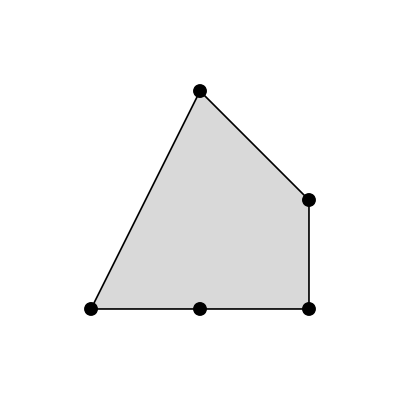

```mathematica
A = {{1,1,1,1, 1},{0,1, 2, 1, 2}, {0, 0, 0, 2, 1}};
Timing[ADiscriminant[A]]
HornKapranov[A]
DualDefectiveQ[A]
CuspidalForm[A]
ConvexHullPlot[A]
```

```mathematica
A = {{1,1,1,1, 1, 1},{0,0, 0, 1, 1, 1}, {0,1,0,0,1,0}, {0,0,1,0,0,1}};
Timing[ADiscriminant[A]]
HornKapranov[A]
DualDefectiveQ[A]
CuspidalForm[A]
```

ADiscriminant::Defective: The point configuration A is dual defective.

{0.003395,$Failed}

{t1+t2,-t2 z2,-t1 z3,(-t1-t2) z1,t2 z1 z2,t1 z1 z3}

True

0